```mathematica
2(3^m-2^m)/((2^(m+n)-3^(m))*2^m)//TraditionalForm
```

(2^(1-m) (3^m-2^m))/(2^(m+n)-3^m)

```mathematica
TraditionalForm[(2(m+n))2(3^m-2^m)/((2^(m+n)-3^(m))*2^m)]
```

(2^(2-m) (3^m-2^m) (m+n))/(2^(m+n)-3^m)

```mathematica
Plot3D[(2(m+n))2(3^m-2^m)/((2^(m+n)-3^(m))*2^m),{n,0,40},{m,0,40}, PlotRange->All, Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[(2^(m+n))2^(1-m)(3^m-2^m)/(2^(m+n)-3^m),{n,0,40},{m,0,40}, PlotRange->All, Mesh->All]
```

-Graphics3D-

```mathematica
Clear[m,n]
```

```mathematica
Simplify[(2(3^m-2^m)/((2^(m+n)-3^(m))*2^m))<1,{m,n}]
```

(2 (-1+(3/2)^True))/(-3^True+4^True)<1

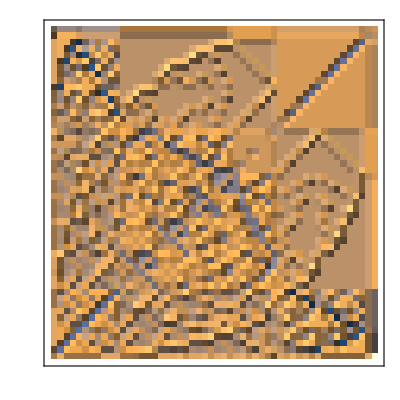

```mathematica
ReliefPlot[ConversionMatrix["C","F"]]
```

```mathematica
FindMaximum[(2(m+n))2(3^m-2^m)/((2^(m+n)-3^(m))*2^m),{n,m}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{8.55845×10^14,{n→0.736732,m→1.25945}}

```mathematica
(2(m+n))2(3^m-2^m)/((2^(m+n)-3^(m))*2^m)/.{n->0.7367319201935632,m->1.259451536269931}
```

8.55845×10^14

```mathematica
GradientFilter
```